```mathematica
Plot3D[{Sin[x+y^2],-0.99},{x,-2,2},{y,-2,2},Filling->Bottom,RegionFunction->(#1^2+#2^2<3&),Axes->False,Boxed->False,ImageSize->600]
```

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]];
nodes3dF = Import["nodes3dF.txt"]//ToExpression;(* 'nodes' array, but with added 3rd dimension to each node, set to 0 (F = floor). *)
nodes3dMF = Import["nodes3dMF.txt"]//ToExpression;(* 'nodesM' array, but with added 3rd dimension to each node, set to 0 (F = floor). *)
nodes3dMT = Import["nodes3dMT.txt"]//ToExpression;(* 'nodesM' array, but with added 3rd dimension to each node, set to 1 (T = top). *)
transNodes3dF = Import["transNodes3dF.txt"]//ToExpression;(* 'transNodes' array, but with added 3rd dimension to each node, set to 0 (F = floor).*)
transNodes3dMF = Import["transNodes3dMF.txt"]//ToExpression;(* 'transNodes' array, but with added 3rd dimension to each node, set to 0 (F = floor).*)
transNodes3dMT = Import["transNodes3dMT.txt"]//ToExpression;(* 'transNodes' array, but with added 3rd dimension to each node, set to 1 (T = top).*)
```

```mathematica
lines3d1=Table[Line[{nodes3dF[[i,1]],nodes3dF[[i,10]]}],{i,1,10,3}];(* Horizontal lines corresponding to grid for 'nodes3dF' *)
lines3d2=Table[Line[{nodes3dF[[1,i]],nodes3dF[[10,i]]}],{i,1,10,3}];(* Vertical lines corresponding to grid for 'nodes3dF' *)
lines3d3=Flatten[(* Z lines connecting grid 'nodes3dF' to grid 'nodes3dT' *)
	Table[
		Line[{nodes3dMF[[i,j]],nodes3dMT[[i,j]]}],
		{i,1,4},
		{j,1,4}],
1];
lines3d=Flatten[{lines3d1,lines3d2},1];(* All lines corresponding to grid 'nodes3dF' *)
lines3dMSpec=Flatten[(* Z lines connecting grid 'nodes3dF' to grid 'nodes3dT' *)
	Table[
		Line[{nodes3dMF[[i,j]],nodes3dMT[[i,j]]}],
		{i,1,4,3},
		{j,1,4,3}],
1];
```

```mathematica
transLines3d1=Table[(* Horizontal lines corresponding to grid for 'transNodes3dF' *)
	Line[Table[transNodes3dF[[i,j]],{j,1,4}]],
	{i,1,4}
];
transLines3d2=Table[(* Vertical lines corresponding to grid for 'transNodes3dF' *)
	Line[Table[transNodes3dF[[j,i]],{j,1,4}]],
	{i,1,4}
];
transLines3d3=Flatten[(* Z lines connecting grid 'transNodes3dF' to grid 'transNodes3dT' *)
	Table[
		Line[{transNodes3dMF[[i,j]],transNodes3dMT[[i,j]]}],
		{i,1,2},
		{j,1,2}],
1];
transLines3d=Flatten[{transLines3d1,transLines3d2},1];(* All lines corresponding to grids 'transNodes3dF' and 'transNodes3dT' *)
g[x_,y_,r0__,σ_]:=Exp[-((x-r0[[1]])^2+(y-r0[[2]])^2)/(2 σ^2)]    (* Custom 2D Gaussian *)
```

```mathematica
nXYGridLines=4;
xYGridLines=Table[{6/(nXYGridLines-1) i-3,Thickness[0.002]} , {i,0,nXYGridLines-1}];
nXZGridLines=3;
xZGridLines=Table[{1/(nXZGridLines-1) i,Thickness[0.002] }, {i,0,nXZGridLines-1}];
nZXGridLines=4;
zXGridLines=Table[{6/(nZXGridLines-1) i-3,Directive[Thickness[0.003],Black]}, {i,0,nZXGridLines-1}];     (* Grid line positions and their individual stylings for the lower plate on the 3D plot. *)
SetOptions[Plot3D,
	AxesLabel->Automatic,
	PlotRange->{{-3,3},{-3,3},{0,1}},
	PlotPoints->{60,60},
	LabelStyle->{FontFamily["DejaVu Math TeX Gyre"],Directive[20,Bold]},
	Ticks->{{-3,-1,1,3},{-3,-1,1,3},Automatic},
	Boxed->False
];
plotVisuals={Lighting["Neutral"],Specularity[White,70],Opacity[0.6]};
plotOptions={};
std=0.5;
meshLineThickness=0.0035;
meshColors={Gray,Gray,Gray,Gray};
stop=3;
plotGauss3d[r0__,std_,color_,opacity_,mesh_]:=Plot3D[
		g[x,y,r0,std],
		{x,r0[[1]]-stop std,r0[[1]]+stop  std},
		{y,r0[[2]]-stop  std,r0[[2]]+stop  std},
		Mesh->{mesh,mesh},
		MeshStyle->Thickness[0.0015],
		PlotStyle->Directive[color,Lighting["Neutral"],Specularity[White,70],opacity],
		RegionFunction->Function[{x,y,z},(x-r0[[1]])^2+(y-r0[[2]])^2<(stop std)^2]]
op={Opacity[0.65],Opacity[0.55],Opacity[0.45],Opacity[0.35]};
```

```mathematica
Show[
	plotGauss3d[nodes[[4,4]], std,RGBColor["#ff8e8e"],op[[4]],0],plotGauss3d[nodes[[5,4]],std,RGBColor["#fdff00"],op[[3]],0],plotGauss3d[nodes[[6,4]], std,RGBColor["#66aaf6"],op[[2]],0],plotGauss3d[nodes[[7,4]],std,RGBColor["#8beb91"],op[[1]],0],
	plotGauss3d[nodes[[4,5]], std,RGBColor["#66aaf6"],op[[4]],0],plotGauss3d[nodes[[5,5]], std,RGBColor["#8beb91"],op[[3]],0],plotGauss3d[nodes[[6,5]], std,RGBColor["#ff8e8e"],op[[2]],0],plotGauss3d[nodes[[7,5]],std,RGBColor["#fdff00"],op[[2]],0],
	plotGauss3d[nodes[[4,6]],std,RGBColor["#ff8e8e"],op[[4]],0],plotGauss3d[nodes[[5,6]],std,RGBColor["#fdff00"],op[[3]],0],plotGauss3d[nodes[[6,6]],std,RGBColor["#66aaf6"],op[[3]],0],plotGauss3d[nodes[[7,6]],std,RGBColor["#8beb91"],op[[3]],0],
	plotGauss3d[nodes[[4,7]],std,RGBColor["#66aaf6"],op[[4]],0],plotGauss3d[nodes[[5,7]],std,RGBColor["#8beb91"],op[[4]],0],plotGauss3d[nodes[[6,7]],std,RGBColor["#ff8e8e"],op[[4]],0],plotGauss3d[nodes[[7,7]],std,RGBColor["#fdff00"],op[[4]],0],
	Graphics3D[{
		Red,PointSize[0.02],Thickness[0.005],
		lines3d3,
		Point[Flatten[nodes3dMF,1]],
		Black,Thickness[0.009],Specularity[White,70],
		lines3d,
		LightBlue, Opacity[0.1],
		Hyperplane[{1,0,0},{-3,0,0}],
		Hyperplane[{0,-1,0},{0,3,0}],
		RGBColor["#a4f2f1"], Opacity[0.6],
		Polygon[{nodes3dF[[1,1]],nodes3dF[[1,4]],nodes3dF[[4,4]],nodes3dF[[4,1]]}],
		Polygon[{nodes3dF[[7,1]],nodes3dF[[7,4]],nodes3dF[[10,4]],nodes3dF[[10,1]]}],
		Polygon[{nodes3dF[[4,4]],nodes3dF[[4,7]],nodes3dF[[7,7]],nodes3dF[[7,4]]}],
		Polygon[{nodes3dF[[1,7]],nodes3dF[[1,10]],nodes3dF[[4,10]],nodes3dF[[4,7]]}],
		Polygon[{nodes3dF[[7,7]],nodes3dF[[7,10]],nodes3dF[[10,10]],nodes3dF[[10,7]]}],
		Black,
		Polygon[{nodes3dF[[4,1]],nodes3dF[[4,4]],nodes3dF[[7,4]],nodes3dF[[7,1]]}],
		Polygon[{nodes3dF[[4,7]],nodes3dF[[4,10]],nodes3dF[[7,10]],nodes3dF[[7,7]]}],
		Polygon[{nodes3dF[[1,4]],nodes3dF[[1,7]],nodes3dF[[4,7]],nodes3dF[[4,4]]}],
		Polygon[{nodes3dF[[7,4]],nodes3dF[[7,7]],nodes3dF[[10,7]],nodes3dF[[10,4]]}]
	}],
	ImageSize->680,
	FaceGrids->{
			{{-1,0,0},{xYGridLines,xZGridLines}},
			{{0,1,0},{xYGridLines,xZGridLines}}
	}
]
```

-Graphics3D-

```mathematica
Show[
	plotGauss3d[nodes[[4,4]], std,RGBColor["#ff8e8e"],op[[4]],6],plotGauss3d[nodes[[7,4]],std,RGBColor["#8beb91"],op[[4]],6],
	plotGauss3d[nodes[[4,7]],std,RGBColor["#66aaf6"],op[[4]],6],plotGauss3d[nodes[[7,7]],std,RGBColor["#fdff00"],op[[4]],6],
	Graphics3D[{
		Red,PointSize[0.02],Thickness[0.005],
		lines3dMSpec,
		Point[Flatten[nodes3dMF,1]],
		Black,Thickness[0.009],Specularity[White,70],
		lines3d,
		LightBlue, Opacity[0.1],
		Hyperplane[{1,0,0},{-3,0,0}],
		Hyperplane[{0,-1,0},{0,3,0}],
		RGBColor["#a4f2f1"], Opacity[0.6],
		Polygon[{nodes3dF[[1,1]],nodes3dF[[1,4]],nodes3dF[[4,4]],nodes3dF[[4,1]]}],
		Polygon[{nodes3dF[[7,1]],nodes3dF[[7,4]],nodes3dF[[10,4]],nodes3dF[[10,1]]}],
		Polygon[{nodes3dF[[4,4]],nodes3dF[[4,7]],nodes3dF[[7,7]],nodes3dF[[7,4]]}],
		Polygon[{nodes3dF[[1,7]],nodes3dF[[1,10]],nodes3dF[[4,10]],nodes3dF[[4,7]]}],
		Polygon[{nodes3dF[[7,7]],nodes3dF[[7,10]],nodes3dF[[10,10]],nodes3dF[[10,7]]}],
		Black,
		Polygon[{nodes3dF[[4,1]],nodes3dF[[4,4]],nodes3dF[[7,4]],nodes3dF[[7,1]]}],
		Polygon[{nodes3dF[[4,7]],nodes3dF[[4,10]],nodes3dF[[7,10]],nodes3dF[[7,7]]}],
		Polygon[{nodes3dF[[1,4]],nodes3dF[[1,7]],nodes3dF[[4,7]],nodes3dF[[4,4]]}],
		Polygon[{nodes3dF[[7,4]],nodes3dF[[7,7]],nodes3dF[[10,7]],nodes3dF[[10,4]]}]
	}],
	ImageSize->680,
	FaceGrids->{
			{{-1,0,0},{xYGridLines,xZGridLines}},
			{{0,1,0},{xYGridLines,xZGridLines}}
	}
]
```

-Graphics3D-

```mathematica
plotOptions2={Mesh->{16,16},MeshStyle->Thickness[0.0015]};
plotVisuals2={Lighting["Neutral"],Specularity[GrayLevel[1],70],Opacity[0.75]};
nXZGridLines2=4.6;
xZGridLines2=Table[{3.6/(nXZGridLines2-1) i,Thickness[0.002] }, {i,0,nXZGridLines2-1}];
Show[
	Plot3D[
		g[x,y,nodes[[4,4]],std]+g[x,y,nodes[[5,4]],std]+g[x,y,nodes[[6,4]],std] +g[x,y,nodes[[7,4]],std]+
		g[x,y,nodes[[4,5]], std]+g[x,y,nodes[[5,5]], std]+g[x,y,nodes[[6,5]], std]+g[x,y,nodes[[7,5]], std]+
		g[x,y,nodes[[4,6]], std]+g[x,y,nodes[[5,6]], std]+g[x,y,nodes[[6,6]], std]+g[x,y,nodes[[7,6]], std]+
		g[x,y,nodes[[4,7]], std]+g[x,y,nodes[[5,7]], std]+g[x,y,nodes[[6,7]], std]+g[x,y,nodes[[7,7]], std],
		{x,-3,3},
		{y,-3,3},
		Evaluate[plotOptions2],
		PlotStyle->Directive[RGBColor["#fdff00"],plotVisuals2],
		PlotRange->{{-3,3},{-3,3},{0,3.6}},
		Boxed->False
	],
	Graphics3D[{
		Red,PointSize[0.02],Thickness[0.005],Opacity[1.0],
		Point[Flatten[nodes3dMF,1]],
		Black,Thickness[0.009],Specularity[White,70],
		lines3d,
		LightBlue, Opacity[0.1],
		Hyperplane[{1,0,0},{-3,0,0}],
		Hyperplane[{0,-1,0},{0,3,0}],
		RGBColor["#a4f2f1"], Opacity[0.5],
		Hyperplane[{0,0,1},{0,0,0}]
	}],
	ImageSize->680,
	FaceGrids->{
			{{-1,0,0},{xYGridLines,xZGridLines2}},
			{{0,1,0},{xYGridLines,xZGridLines2}}
	}
]
```

-Graphics3D-

```mathematica
plotOptions3={Mesh->{3,3},MeshStyle->Thickness[0.0012]};
plotVisuals3={Lighting["Neutral"],Specularity[GrayLevel[1],70],Opacity[0.75]};
plotElmFunc[r0__,f_,color_]:=
	Plot3D[
		g[x,y,r0,std],
		{x,r0[[1]]-stop std,r0[[1]]+stop  std},
		{y,r0[[2]]- stop std,r0[[2]]+stop std},
		Evaluate[plotOptions3],
		PlotStyle->Directive[color,plotVisuals3],
		RegionFunction->Function[{x,y,z},(x-r0[[1]])^2+(y-r0[[2]])^2<(stop std)^2 && f[x,y]]
	]
Show[
	plotElmFunc[nodes[[4,4]],(#1>-1 && #2>-1)&,RGBColor["#ff8e8e"]],
	plotElmFunc[nodes[[7,4]],(#1>-1 && #2<1)&,RGBColor["#8beb91"]],
	plotElmFunc[nodes[[4,7]],(#1<1 && #2>-1)&,RGBColor["#66aaf6"]],
	plotElmFunc[nodes[[7,7]],(#1<1 && #2<1)&,RGBColor["#fdff00"]],
	Graphics3D[{
		Red,PointSize[0.025],Thickness[0.005],
		lines3dMSpec,
		Point[Flatten[nodes3dF,1]],
		Black,Thickness[0.02],Specularity[White,70],
		lines3d,
		LightBlue, Opacity[0.1],
		Hyperplane[{1,0,0},{-1.5,0,0}],
		Hyperplane[{0,-1,0},{0,1.5,0}],
		RGBColor["#a4f2f1"], Opacity[0.6],
		Polygon[{nodes3dF[[1,1]],nodes3dF[[1,4]],nodes3dF[[4,4]],nodes3dF[[4,1]]}],
		Polygon[{nodes3dF[[7,1]],nodes3dF[[7,4]],nodes3dF[[10,4]],nodes3dF[[10,1]]}],
		Polygon[{nodes3dF[[4,4]],nodes3dF[[4,7]],nodes3dF[[7,7]],nodes3dF[[7,4]]}],
		Polygon[{nodes3dF[[1,7]],nodes3dF[[1,10]],nodes3dF[[4,10]],nodes3dF[[4,7]]}],
		Polygon[{nodes3dF[[7,7]],nodes3dF[[7,10]],nodes3dF[[10,10]],nodes3dF[[10,7]]}],
		Black,
		Polygon[{nodes3dF[[4,1]],nodes3dF[[4,4]],nodes3dF[[7,4]],nodes3dF[[7,1]]}],
		Polygon[{nodes3dF[[4,7]],nodes3dF[[4,10]],nodes3dF[[7,10]],nodes3dF[[7,7]]}],
		Polygon[{nodes3dF[[1,4]],nodes3dF[[1,7]],nodes3dF[[4,7]],nodes3dF[[4,4]]}],
		Polygon[{nodes3dF[[7,4]],nodes3dF[[7,7]],nodes3dF[[10,7]],nodes3dF[[10,4]]}]
	}],
	PlotRange->{{-1.5,1.5},{-1.5,1.5},{0,1}},
	PlotPoints->{100,100},
	LabelStyle->{FontFamily["DejaVu Math TeX Gyre"],Directive[20,Bold]},
	Ticks->{{-3,-1,1,3},{-3,-1,1,3},{0,1}},
	BoxRatios->{1,1,0.55},
	Boxed->False,
	AxesLabel->{ξ,η,z},
	ImageSize->650,
	FaceGrids->{
			{{-1,0,0},{xYGridLines,xZGridLines}},
			{{0,1,0},{xYGridLines,xZGridLines}}
	}
]
```

-Graphics3D-

```mathematica
nodes3dMF[[1,1]]
nodes3dMF[[1,4]]
nodes3dMF[[4,4]]
nodes3dMF[[4,1]]
```

{-1,-1,0}

{1,-1,0}

{1,1,0}

{-1,1,0}

```mathematica
(* Quadrilateral shape functions.*)
Subscript[S, 1][ξ_,η_]:= 1/4(1-ξ)(1-η)
Subscript[S, 2][ξ_,η_]:= 1/4(1+ξ)(1-η)
Subscript[S, 3][ξ_,η_]:= 1/4(1+ξ)(1+η)
Subscript[S, 4][ξ_,η_]:= 1/4(1-ξ)(1+η)
(* Transformation functions from fundamental square to deformed quadrilateral. *)
P[ξ_,η_]:=  transNodesM[[1,1]] Subscript[S, 1][ξ,η]+transNodesM[[1,4]] Subscript[S, 2][ξ,η]+transNodesM[[4,4]] Subscript[S, 3][ξ,η]+transNodesM[[4,1]] Subscript[S, 4][ξ,η]
P[1,1]
```

{0.931471,0.98572}

```mathematica
plotVisuals4={Lighting["Neutral"],Specularity[GrayLevel[1],70],Opacity[0.6]};
Show[
	Plot3D[
		g[x,y,nodesT[[6,1]],nodesT[[6,2]],stds[[1]]],
		{x,nodesT[[6,1]]-2.7 stds[[1]],nodesT[[6,1]]+2.7  stds[[1]]},
		{y,nodesT[[6,2]]-2.7  stds[[1]],nodesT[[6,2]]+2.7  stds[[1]]},
		PlotStyle->Directive[RGBColor["#ff8e8e"],plotVisuals4],
		RegionFunction->Function[{x,y,z},(x-nodesT[[6,1]])^2+(y-nodesT[[6,2]])^2<(2.7 stds[[1]])^2]
	],
	Plot3D[
		g[x,y,nodesT[[7,1]],nodesT[[7,2]],stds[[2]]],
		{x,nodesT[[7,1]]-2.7 stds[[2]],nodesT[[7,1]]+2.7 stds[[2]]},
		{y,nodesT[[7,2]]-2.7 stds[[2]],nodesT[[7,2]]+2.7 stds[[2]]},
		PlotStyle->Directive[RGBColor["#8beb91"],plotVisuals4],
		RegionFunction->Function[{x,y,z},(x-nodesT[[7,1]])^2+(y-nodesT[[7,2]])^2<(2.7 stds[[2]])^2]
	],
	Plot3D[
		g[P[ξ,η],Q[ξ,η],0,0,stds[[3]]],
		{x,nodesT[[10,1]]-2.7 stds[[3]],nodesT[[10,1]]+2.7 stds[[3]]},
		{y,nodesT[[10,2]]-2.7 stds[[3]],nodesT[[10,2]]+2.7 stds[[3]]},
		PlotStyle->Directive[RGBColor["#66aaf6"],plotVisuals4],
		RegionFunction->Function[{x,y,z},(x-nodesT[[10,1]])^2+(y-nodesT[[10,2]])^2<(2.7 stds[[3]])^2]
	],
	Plot3D[
		g[x,y,nodesT[[11,1]],nodesT[[11,2]],stds[[4]]],
		{x,nodesT[[11,1]]-2.7 stds[[4]],nodesT[[11,1]]+2.7 stds[[4]]},
		{y,nodesT[[11,2]]-2.7 stds[[4]],nodesT[[11,2]]+2.7 stds[[4]]},
		PlotStyle->Directive[RGBColor["#d5d87d"],plotVisuals4],
		RegionFunction->Function[{x,y,z},(x-nodesT[[11,1]])^2+(y-nodesT[[11,2]])^2<(2.7 stds[[4]])^2]
	],
	Graphics3D[{
		Red,PointSize[0.03],Thickness[0.009],
		Table[Line[{nodesMidHT[[i]],nodesMidGT[[i]]}],{i,1,Length[nodesMidGT]}],
		Point[nodesHT],
		Black,Thickness[0.009],Specularity[White,70],
		floorLinesT,
		LightBlue, Opacity[0.1],
		Hyperplane[{1,0,0},{0,0,0}],
		Hyperplane[{0,-1,0},{0,3,0}],
		RGBColor["#a4f2f1"], Opacity[0.5],
		Hyperplane[{0,0,1},{0,0,0}]
	}],
	ImageSize->600,
	FaceGrids->{
			{{-1,0,0},{xYGridLines,xZGridLines}},
			{{0,1,0},{xYGridLines,xZGridLines}}(*,
			{{0,0,-1},{zXGridLines,zXGridLines}}*)
	}
]
```

-Graphics3D-

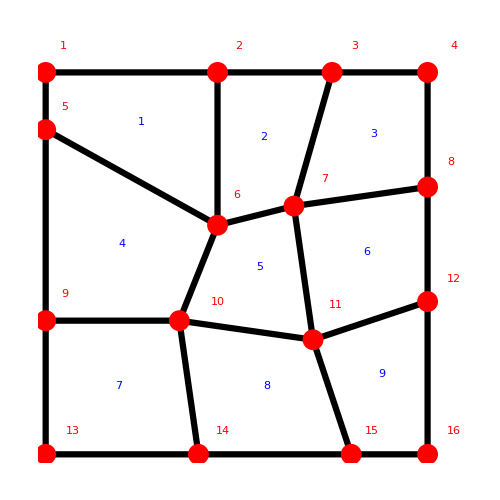

```mathematica
Graphics[{
	Black,Thickness[0.009],
	linesT,
	Red,PointSize[0.03],
	Point[nodesT],
	FontSize->36,Red,
	Text[13,{3 0.07,3 0.06}], Text[14,{3 0.465,3 0.06}], Text[15,{3 0.855,3 0.06}],Text[16,{3 1.07,3 0.06}],
	Text[9,{3 0.05,3 0.42}],Text[10,{3 0.45,3 0.40}],Text[11,{3 0.76,3 0.39}],Text[12,{3 1.07,3 0.46}],
	Text[5,{3 0.05,3 0.91}],Text[6,{3 0.50,3 0.68}],Text[7,{3 0.73,3 0.72}],Text[8,{3 1.06,3 0.765}],
	Text[1,{3 0.045,3 1.07}],Text[2,{3 0.505,3 1.07}],Text[3,{3 0.81,3 1.07}],Text[4,{3 1.07,3 1.07}],
	FontSize->70,Blue,
	Text[1,{3 0.25,3 0.87}],Text[2,{3 0.57,3 0.83}],Text[3,{3 0.86,3 0.84}],
	Text[4,{3 0.20,3 0.55}],Text[5,{3 0.56,3 0.49}],Text[6,{3 0.84,3 0.53}],
	Text[7,{3 0.19,3 0.18}],Text[8,{3 0.58,3 0.18}],Text[9,{3 0.88,3 0.21}]
},ImageSize->500]
```

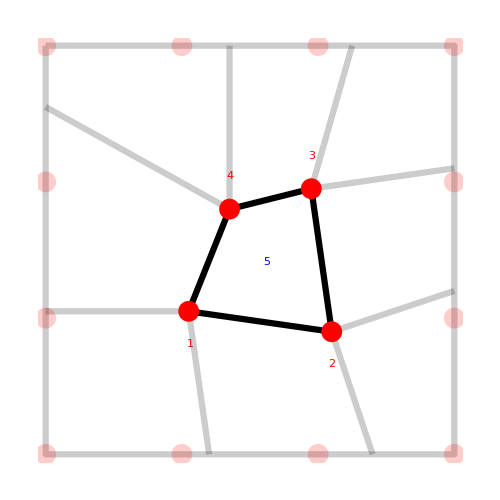

```mathematica
nodesMidT={nodesT[[6]],nodesT[[7]],nodesT[[10]],nodesT[[11]]};
nodesMid={nodes[[6]],nodes[[7]],nodes[[10]],nodes[[11]]};
otherNodes={nodes[[1]],nodes[[2]],nodes[[3]],nodes[[4]],nodes[[5]],nodes[[8]],nodes[[9]],nodes[[12]],nodes[[13]],nodes[[14]],nodes[[15]],nodes[[16]]};
otherNodesT={nodesT[[1]],nodesT[[2]],nodesT[[3]],nodesT[[4]],nodesT[[5]],nodesT[[8]],nodesT[[9]],nodesT[[12]],nodesT[[13]],nodesT[[14]],nodesT[[15]],nodesT[[16]]};
linesMid={Line[{nodes[[6]],nodes[[7]],nodes[[11]],nodes[[10]],nodes[[6]]}]};
linesMidT={Line[{nodesT[[6]],nodesT[[7]],nodesT[[11]],nodesT[[10]],nodesT[[6]]}]};
otherLines={
	Line[{nodes[[1]],nodes[[4]],nodes[[16]],nodes[[13]],nodes[[1]]}],
	Line[{nodes[[2]],nodes[[6]]}],
	Line[{nodes[[3]],nodes[[7]]}],
	Line[{nodes[[7]],nodes[[8]]}],
	Line[{nodes[[11]],nodes[[12]]}],
	Line[{nodes[[11]],nodes[[15]]}],
	Line[{nodes[[10]],nodes[[14]]}],
	Line[{nodes[[9]],nodes[[10]]}],
	Line[{nodes[[5]],nodes[[6]]}]
};
otherLinesT={
	Line[{nodesT[[1]],nodesT[[4]],nodesT[[16]],nodesT[[13]],nodesT[[1]]}],
	Line[{nodesT[[2]],nodesT[[6]]}],
	Line[{nodesT[[3]],nodesT[[7]]}],
	Line[{nodesT[[7]],nodesT[[8]]}],
	Line[{nodesT[[11]],nodesT[[12]]}],
	Line[{nodesT[[11]],nodesT[[15]]}],
	Line[{nodesT[[10]],nodesT[[14]]}],
	Line[{nodesT[[9]],nodesT[[10]]}],
	Line[{nodesT[[5]],nodesT[[6]]}]
};
Graphics[{
	Black,Thickness[0.009],
	linesMidT,
	Opacity[0.2],
	otherLinesT,
	Opacity[1.0],
	Red,PointSize[0.03],
	Point[nodesMidT],
	Opacity[0.2],
	Point[otherNodes],
	Opacity[1.0],FontSize->70,Blue,
	Text[5,{3 0.54,3 0.47}],
	FontSize->42,Red,
	Text[4,{3 0.45,3 0.68}],Text[3,{3 0.65,3 0.73}],Text[1,{3 0.355,3 0.27}],Text[2,{3 0.70,3 0.22}]
	},
	ImageSize->500]
```

```mathematica
(*  *)
```